```mathematica
Sum[ (-1)^j/((2 j)!) x^(-2 j s),{j,0,Infinity}]
```

Cos[x^-s]

```mathematica
FullSimplify[Sum[ (-1)^j/((2 j)!) x^(-2 j s),{j,0,n}]]
```

Cos[x^-s]+((-1)^n x^(-2 (1+n) s) HypergeometricPFQ[{1},{3/2+n,2+n},-1/4 x^(-2 s)])/Gamma[3+2 n]

```mathematica
N@Sum[ ((-1)^j/((2 j)!) x^(-2 j s))((-1)^k/((2 k)!) x^(-2 k s)),{j,0,10}, {k,0,10}]/.s->0
```

0.291927

```mathematica
N[Cos[1]^2]
```

0.291927

```mathematica
Plot[Cos[2.^-s],{s,-15,15}]
```

```mathematica
Sum[ (-1)^k Binomial[z,k] x^(-s k),{k,0,Infinity}]
```

(1-x^-s)^z

```mathematica
Sum[ (-1)^k z^k/(k!)  x^(-s k),{k,0,Infinity}]
```

ⅇ^(-x^-s z)

```mathematica
FI[n_]:=FactorInteger[n];FI[1]:={}
dzo[n_,z_]:=Product[Pochhammer[z,p[[2]]]/(p[[2]]!),{p,FI[n]}]
dz[n_,z_]:=dz[n,z]=Product[z^p[[2]] /(p[[2]]!),{p,FI[n]}]
```

```mathematica
Table[D[dz[n,z],z]/.z->0,{n,1,10}]//TableForm
```

0
-1
-1
1/2
-1
0
-1
-1/3
1/2
0

```mathematica
FullSimplify[ ((1-x^(-4s))/(1-x^(-s)))^z]
```

(x^(-3 s) (1+x^s) (1+x^(2 s)))^z

```mathematica
Expand[x^(-3 s) (1+x^s) (1+x^(2 s))]
```

1+x^(-3 s)+x^(-2 s)+x^-s

```mathematica
Sum[ Pochhammer[z,k]/k! x^(-s k),{k,0,Infinity}]
```

(1-x^-s)^-z

```mathematica
Sum[ Pochhammer[-z,k]/k! x^(-2s k),{k,0,Infinity}]
```

(1-x^(-2 s))^z

```mathematica
Limit[FullSimplify[ ((1-x^(-a s))/(1-x^(-s)))^z],x->1]
```

a^z

```mathematica
Limit[FullSimplify[ ((1-x^(-a s))/(1-x^(-s)))^z],s->0]
```

a^z

```mathematica
D[((1-x^(-a s))/(1-x^(-s)))^z,z]/.z->0
```

Log[(1-x^(-a s))/(1-x^-s)]

```mathematica
Limit[Log[(1-x^(-a s))/(1-x^-s)],s->0]
```

Log[a]

```mathematica
Clear[p2,pm,do2]
bin[z_,k_]:=bin[z,k]=Product[z-j,{j,0,k-1}]/k!
do2[n_,s_,k_]:=do2[n,s,k]=Sum[j^-s do2[Floor[n/j],s,k-1],{j,2,n}]
do2[n_,s_,0]:=UnitStep[n-1]
doz[n_,s_,z_]:=Sum[bin[z,k]do2[n,s,k],{k,0,Log2@n}]
p2[n_,s_,k_]:=p2[n,s,k]=Sum[(-1)^(j+1)j^-s p2[Floor[n/j],s,k-1],{j,2,n}]
p2[n_,s_,0]:=UnitStep[n-1]
pz[n_,s_,z_]:=Sum[bin[z,k]p2[n,s,k],{k,0,Log2@n}]
pm[n_,s_]:=pm[n,s]=Sum[ MoebiusMu[ k]/k D[pz[n^(1/k),s,z],z]/.z->0,{k,1,Log2@n}]
pmi[n_,s_]:=Sum[ 1/k pm[n^(1/k),s],{k,1,Log2@n}]
pd[1,s_]:=0
pd[n_,s_]:=pm[n,s]-pm[n-1,s]
pdk[n_,s_,k_]:=pdk[n,s,k]=Sum[pd[j,s]pdk[Floor[n/j],k-1],{j,2,n}]
pdk[n_,s_,0]:=UnitStep[n-1]
pdz[n_,s_,z_]:=Sum[z^k/k! pdk[n,s,k],{k,0,Log2@n}]
pmx[n_,s_]:=Sum[ MoebiusMu[ k]/k D[pz[n^(1/k),s,z]-doz[n^(1/k),s,z],z]/.z->0,{k,1,Log2@n}]
```

```mathematica
Table[ pm[n,0]-pm[n-1,0],{n,2,100}]
```

{-1,1,-1,1,0,1,-2,0,0,1,0,1,0,0,-3,1,0,1,0,0,0,1,0,0,0,0,0,1,0,1,-6,0,0,0,0,1,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,-9,0,0,1,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0}

```mathematica
(* https://oeis.org/A001037 *)
(* https://oeis.org/A059966 *)
```

```mathematica
Table[ (pm[2^k,0]-pm[2^k-1,0]),{k,1,16}]
```

{-1,-1,-2,-3,-6,-9,-18,-30,-56,-99,-186,-335,-630,-1161,-2182,-4080}

```mathematica
Table[ (pm2[n,0]-pm2[n-1,0]),{n,2,100}]
```

{-2,0,-1,0,0,0,-2,0,0,0,0,0,0,0,-3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-6,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[D[(pz[n,0,z]-doz[n,0,z])-(pz[n-1,0,z]-doz[n-1,0,z]),z]/.z->0,{n,2,100}]
```

{-2,0,-2,0,0,0,-8/3,0,0,0,0,0,0,0,-4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-32/5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-32/3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[pd[n,0],{n,1,100}]
```

{0,-1,1,-1,1,0,1,-2,0,0,1,0,1,0,0,-3,1,0,1,0,0,0,1,0,0,0,0,0,1,0,1,-6,0,0,0,0,1,0,0,0,1,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,1,0,1,0,0,-9,0,0,1,0,0,0,1,0,1,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0}

```mathematica
FullSimplify[Table[ Sum[ MoebiusMu[n/d]((2^d)-1)/n,{d,Divisors[n]}],{n,1,16}]]
```

{1,1,2,3,6,9,18,30,56,99,186,335,630,1161,2182,4080}

```mathematica
Table[ N@(2^n-1)/n,{n,1,16}]
```

{1.,1.5,2.33333,3.75,6.2,10.5,18.1429,31.875,56.7778,102.3,186.091,341.25,630.077,1170.21,2184.47,4095.94}

```mathematica
Table[ (pm[2^k,-1]-pm[2^k-1,-1]),{k,1,16}]
```

{-2,-5,-18,-57,-198,-661,-2322,-8130,-29064,-104655,-381114,-1397405,-5161590,-19171629,-71580534,-268427280}

```mathematica
FullSimplify[Table[  Sum[ MoebiusMu[n/d]((2^d)-1)/n,{d,Divisors[n]}],{n,1,16}]]
```

{1,1,2,3,6,9,18,30,56,99,186,335,630,1161,2182,4080}

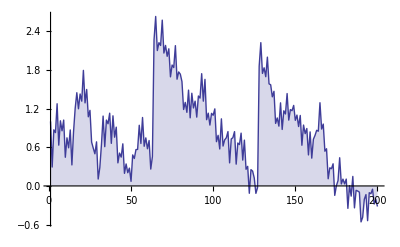

```mathematica
DiscretePlot[Re[pdz[n,.5,1]],{n,1,200}]
```

```mathematica
f[n_]:=Block[{d=Divisors@n},Plus@@(MoebiusMu[n/d]*2^d/n)];Array[f,32]
```

{2,1,2,3,6,9,18,30,56,99,186,335,630,1161,2182,4080,7710,14532,27594,52377,99858,190557,364722,698870,1342176,2580795,4971008,9586395,18512790,35790267,69273666,134215680}

```mathematica
Table[pdz[n,.5,1],{n,1,100}]
```

{1,0.292893,0.870243,0.82735,1.27456,0.632335,1.0103,0.85497,1.02164,0.444476,0.745988,0.591016,0.868367,0.325831,0.838113,1.20326,1.44579,1.1965,1.42591,1.31432,1.79198,1.28767,1.49618,1.07206,1.17206,0.679832,0.586752,0.498243,0.683939,0.106715,0.28632,0.644111,1.08354,0.608721,1.02131,0.964012,1.12841,0.66015,1.0875,0.755559,0.911733,0.357592,0.510091,0.447066,0.653047,0.195237,0.341102,0.204804,0.276232,0.0711132,0.481056,0.426085,0.563446,0.566634,0.940996,0.658106,1.06149,0.615088,0.745277,0.576454,0.704491,0.261135,0.455575,2.26582,2.62811,2.09945,2.22162,2.17825,2.57119,2.06042,2.1791,2.0101,2.12714,1.69139,1.87488,1.83589,2.17562,1.65502,1.76753,1.73317,1.61719,1.18555,1.29531,1.14092,1.48579,1.05599,1.43751,1.20878,1.31477,1.06682,1.39447,1.36245,1.74093,1.31444,1.65275,1.02722,1.12876,0.943694,1.12539,1.09574}

```mathematica
Table[ (pm[2^k,0]-pm[2^k-1,0]),{k,1,12}]
```

{-1,-1,-2,-3,-6,-9,-18,-30,-56,-99,-186,-335}

```mathematica
Table[pmi[n,0],{n,2,40}]
```

{-1,0,-3/2,-1/2,-1/2,1/2,-11/6,-4/3,-4/3,-1/3,-1/3,2/3,2/3,2/3,-37/12,-25/12,-25/12,-13/12,-13/12,-13/12,-13/12,-1/12,-1/12,5/12,5/12,3/4,3/4,7/4,7/4,11/4,-69/20,-69/20,-69/20,-69/20,-69/20,-49/20,-49/20,-49/20,-49/20}

```mathematica
Table[D[pz[n,0,z],z]/.z->0,{n,2,40}]
```

{-1,0,-3/2,-1/2,-1/2,1/2,-11/6,-4/3,-4/3,-1/3,-1/3,2/3,2/3,2/3,-37/12,-25/12,-25/12,-13/12,-13/12,-13/12,-13/12,-1/12,-1/12,5/12,5/12,3/4,3/4,7/4,7/4,11/4,-69/20,-69/20,-69/20,-69/20,-69/20,-49/20,-49/20,-49/20,-49/20}

```mathematica
Table[-z Pochhammer[1-k,n]Pochhammer[1-z,n]/Pochhammer[2,n]  (-1)^n/n!,{n,0,6}]/.k->5//TableForm
```

-z
-2 (1-z) z
-(1-z) (2-z) z
-1/6 (1-z) (2-z) (3-z) z
-1/120 (1-z) (2-z) (3-z) (4-z) z
0
0

```mathematica
Table[-z Pochhammer[1-z,n] Pochhammer[1-k,n] (-1)^n/n!/(n+1)!,{n,0,6}]/.k->5//TableForm
```

-z
-2 (1-z) z
-(1-z) (2-z) z
-1/6 (1-z) (2-z) (3-z) z
-1/120 (1-z) (2-z) (3-z) (4-z) z
0
0

```mathematica
Table[{(-1)^n Pochhammer[1-k,n]/n!,Binomial[k-1,n]},{n,0,6}]/.k->5//TableForm
```

1 | 1
4 | 4
6 | 6
4 | 4
1 | 1
0 | 0
0 | 0

```mathematica
Table[-z Pochhammer[1-z,n]/(n+1)! Binomial[k-1,n],{n,0,6}]/.k->5//TableForm
```

-z
-2 (1-z) z
-(1-z) (2-z) z
-1/6 (1-z) (2-z) (3-z) z
-1/120 (1-z) (2-z) (3-z) (4-z) z
0
0

```mathematica
Table[{Expand[(-z Pochhammer[1-z,n]/(n+1)!)-(-1)^(n+1)(bin[z,n+1])]},{n,0,5}]//TableForm
```

0
0
0
0
0
0

```mathematica
Table[{Expand[(-z Pochhammer[1-z,n]/(n+1)!)-(-1)^(n+1)(bin[z,n+1])]},{n,0,5}]//TableForm
```

```mathematica
Table[(-1)^(n+1)(Binomial[z,n+1]) Binomial[k-1,n],{n,0,6}]/.k->5//TableForm
```

-z
2 (-1+z) z
-(-2+z) (-1+z) z
1/6 (-3+z) (-2+z) (-1+z) z
-1/120 (-4+z) (-3+z) (-2+z) (-1+z) z
0
0

```mathematica
FullSimplify[(-1)^(n+1)(Binomial[z,n+1]) Binomial[k-1,n]]
```

-(-1)^n Binomial[-1+k,n] Binomial[z,1+n]

```mathematica
Table[ (pm[2^k,1]-pm[2^k-1,1]),{k,1,12}]
```

{-1/2,-1/8,-1/8,-3/64,-3/32,3/128,-9/128,-15/2048,-7/512,45/2048,-93/2048,235/16384}

```mathematica
Table[ (pmx[2^k,2]-pmx[2^k-1,2]),{k,1,12}]
```

{-1/2,1/8,1/8,3/64,3/32,-3/128,9/128,15/2048,7/512,-45/2048,93/2048,-235/16384}

```mathematica
Table[ (pm[2^k,2]-pm[2^k-1,2]),{k,1,12}]
```

{-1/4,1/32,3/64,33/1024,45/1024,43/8192,567/16384,3585/524288,3129/262144,-6963/2097152,95139/4194304,-636245/67108864}

```mathematica
eta[s2_]:=Limit[ (1-2^(1-s))Zeta[s],s->s2]
einv[s_]:=Product[ Limit[eta[k s]^(MoebiusMu[k]/k),k->k2],{k2,1,Infinity}]
einv[s_,t_]:=Product[ eta[k s]^(MoebiusMu[k]/k),{k,1,t}]
einv2[s_,t_]:=Product[Limit[ eta[k s]^(MoebiusMu[k]/k),k->k2],{k2,1,t}]
```

```mathematica
eta[1]
```

Log[2]

```mathematica
einv[1]
```

∏_(k2=1)^∞ Limit[(2^-k (-2+2^k) Zeta[k])^(MoebiusMu[k]/k),k→k2]

```mathematica
N@einv[1,80]
```

0.794536

```mathematica
N@einv[2,80]
```

0.849401

```mathematica
N@einv[.5,120]
```

0.811298

```mathematica
N@einv[N[ZetaZero[1]],120]
```

0.+0. ⅈ

```mathematica
N@einv[N[ZetaZero[1]/6],120]
```

0.+0. ⅈ

```mathematica
N[ZetaZero[1]/6]
```

0.0833333+2.35579 ⅈ

```mathematica
N@einv[0.5+14.134725141734695 ⅈ,120]
```

0.+0. ⅈ

```mathematica
N@ZetaZero[1]
```

0.5+14.1347 ⅈ

```mathematica
FullSimplify[(1-2^(1-s)) (1/(1-2^-s))]
```

1+1/(1-2^s)

```mathematica
fs[s_]:=(1+1/(1-2^s))
fs2[s_]:=1+1/(-1+2^s)
eta[s_]:=(1-2^(1-s))Zeta[s]
```

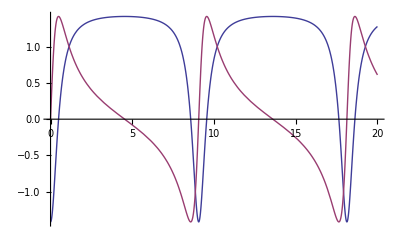

```mathematica
Plot[{Re[ fs[.5+t I]],Im[ fs[.5+t I]]},{t,0,20}]
```

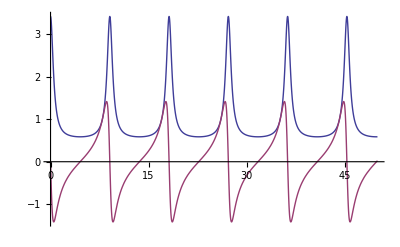

```mathematica
Plot[{Re[ fs2[.5+t I]],Im[ fs2[.5+t I]]},{t,0,50}]
```

```mathematica
FullSimplify@Sum[ 2^(-s k)(-1) Hypergeometric2F1[ 1-k,0,2,-1],{k,0,Infinity}]
```

1/(-1+2^-s)

```mathematica
FullSimplify@Sum[2^(-s k)Pochhammer[1,k]/k!,{k,0,Infinity}]
```

1+1/(-1+2^s)

```mathematica
FullSimplify@Sum[2^(-s k),{k,0,Infinity}]
```

1+1/(-1+2^s)

```mathematica
(-1) Hypergeometric2F1[ 1-k,0,2,-1]
```

-1

```mathematica
FullSimplify[(1/(-1+2^-s))/(1+1/(-1+2^s))]
```

-1

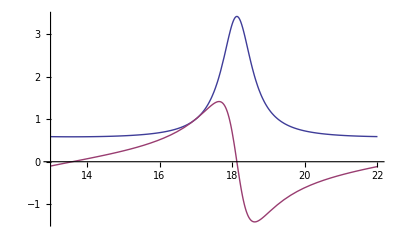

```mathematica
Plot[{Re[ fs2[.5+t I]],Im[ fs2[.5+t I]]},{t,13,22}]
```

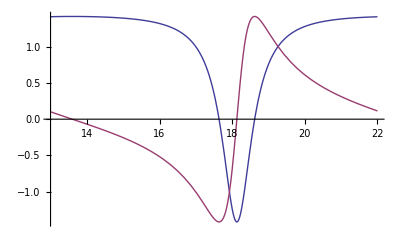

```mathematica
Plot[{Re[ fs[.5+t I]],Im[ fs[.5+t I]]},{t,13,22}]
```

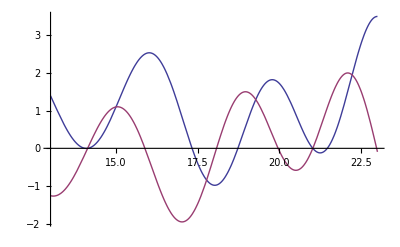

```mathematica
Plot[{Re[ eta[.5+t I]],Im[ eta[.5+t I]]},{t,13,23}]
```

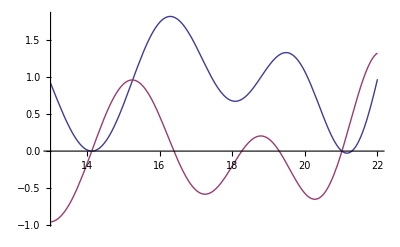

```mathematica
Plot[{Re[  eta[.5+t I]/fs[.5+t I]],Im[ eta[.5+t I]/fs[.5+t I]]},{t,13,22}]
```

```mathematica
ps1[s_]:=Product[ 1/(1-Prime[j]^-s),{j,1,6000}]
ps2[s_]:=Product[ 1/(1-Prime[j]^-s),{j,2,6000}]
ps3[s_]:=(1+1/(1-2^s)) ps2[s]
```

```mathematica
N@{ps1[.5],ps2[.5],ps3[.5]}
```

{4.48127×10^25,1.31253×10^25,-1.8562×10^25}

```mathematica
N@Pi^2/12
```

0.822467

```mathematica
FullSimplify[1-Sum[2^(-s k),{k,1,Infinity}]]
```

1+1/(1-2^s)

```mathematica
Table[ If[a==0,1,-1]Abs[N@(2^a)^-s],{a,0,18}]/.s->.5//TableForm
```

1.
-0.707107
-0.5
-0.353553
-0.25
-0.176777
-0.125
-0.0883883
-0.0625
-0.0441942
-0.03125
-0.0220971
-0.015625
-0.0110485
-0.0078125
-0.00552427
-0.00390625
-0.00276214
-0.00195313

```mathematica
Sum[ If[a==0,1,-1]N@(2^a)^-s,{a,0,100}]/.s->N@ZetaZero[4]
```

1.39481+0.233473 ⅈ

```mathematica
N[-2^(1/2)]
```

-1.41421

```mathematica
1-Sum[(2^a)^-s,{a,1,Infinity}]/.s->1/2
```

1-1/(-1+√2)

```mathematica
1-Sum[(2^a)^-s,{a,1,Infinity}]/.s->1/2
```

```mathematica
et[n_,s_]:=Sum[ (-1)^(j+1) j^-s,{j,1,n}]
pom[n_,s_]:=Sum[ j^-s,{j,1,Floor[n]}]
po[n_,s_]:=Sum[ j^-s,{j,1,n,2}]
poi[n_,o_,s_]:=Sum[ (j+o)^-s,{j,1,n,2}]
pox[n_,s_]:=Sum[ (2j+1)^-s,{j,0,(n-1)/2}]
poxy[n_,s_]:=Sum[ (2j-1)^-s,{j,1,(n+1)/2}]
s2[n_,s_]:=po[n,s]-Sum[ (2^a)^-s po[n/(2^a),s],{a,1,Log2@n}]
s2a[n_,s_]:=Sum[ If[a==0,1,-1](2^a)^-s po[n/(2^a),s],{a,0,Log2@n}]
s2aa[n_,s_]:=Sum[ If[a==0,1,-1]Abs[(2^a)^-s po[n/(2^a),s]],{a,0,Log2@n}]
s2t[n_,s_]:=Table[ If[a==0,1,-1](2^a)^-s po[n/(2^a),s],{a,0,Log2@n}]
s2ta[n_,s_]:=Table[ Abs[If[a==0,1,-1](2^a)^-s po[n/(2^a),s]],{a,0,Log2@n}]
s2tx[n_,s_]:=Table[ If[a==0,1,-1]po[n,s]/((2^a)^-s po[n/(2^a),s]),{a,0,Log2@n}]
```

```mathematica
po[1000000,1.]
```

7.54294

```mathematica
s2a[1000000.,-.2+N[ZetaZero[1]]]
```

-0.450893+0.028744 ⅈ

```mathematica
s2a[1000000000.,N[ZetaZero[11]]]
```

0.0000335657-0.000121956 ⅈ

```mathematica
s2t[1000000000000000.,N[ZetaZero[1]]]//TableForm
```

-1.07245×10^6-315585. ⅈ
536226.+157793. ⅈ
268113.+78896.4 ⅈ
134056.+39448.2 ⅈ
67028.2+19724.1 ⅈ
33514.1+9862.05 ⅈ
16757.1+4931.02 ⅈ
8378.53+2465.51 ⅈ
4189.27+1232.76 ⅈ
2094.63+616.378 ⅈ
1047.32+308.189 ⅈ
523.658+154.094 ⅈ
261.829+77.0472 ⅈ
130.915+38.5236 ⅈ
65.4573+19.2618 ⅈ
32.7286+9.6309 ⅈ
16.3643+4.81545 ⅈ
8.18216+2.40773 ⅈ
4.09108+1.20386 ⅈ
2.04554+0.601932 ⅈ
1.02277+0.300966 ⅈ
0.511385+0.150483 ⅈ
0.255692+0.0752414 ⅈ
0.127846+0.0376207 ⅈ
0.0639231+0.0188103 ⅈ
0.0319616+0.00940517 ⅈ
0.0159808+0.00470258 ⅈ
0.00799039+0.00235128 ⅈ
0.0039952+0.00117563 ⅈ
0.0019976+0.000587811 ⅈ
0.000998796+0.000293921 ⅈ
0.000499403+0.000146945 ⅈ
0.000249696+0.0000734876 ⅈ
0.000124853+0.0000367288 ⅈ
0.0000624266+0.0000183644 ⅈ
0.0000312133+9.1822×10^-6 ⅈ
0.0000156067+4.5911×10^-6 ⅈ
7.80333×10^-6+2.29555×10^-6 ⅈ
3.90167×10^-6+1.14778×10^-6 ⅈ
1.9458×10^-6+5.88878×10^-7 ⅈ
9.77923×10^-7+2.79446×10^-7 ⅈ
4.83907×10^-7+1.54708×10^-7 ⅈ
2.4695×10^-7+6.23483×10^-8 ⅈ
1.23713×10^-7+3.12341×10^-8 ⅈ
5.60222×10^-8+3.04206×10^-8 ⅈ
2.89334×10^-8+1.56981×10^-8 ⅈ
1.65695×10^-8+8.85779×10^-9 ⅈ
1.55246×10^-9-1.46302×10^-8 ⅈ
-1.97674×10^-8-1.75985×10^-8 ⅈ
3.50478×10^-8+2.34095×10^-8 ⅈ

```mathematica
po[1000000000,N@ZetaZero[3]]
```

22.843-631.642 ⅈ

```mathematica
2^N[1-ZetaZero[3]] po[1000000000/2,N@ZetaZero[3]]
```

22.843-631.642 ⅈ

```mathematica
4^N[1-ZetaZero[3]] po[1000000000/4,N@ZetaZero[3]]
```

22.8429-631.642 ⅈ

```mathematica
Table[ po[n,.5]-poxy[n,.5],{n,1,10}]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(1^N[1-ZetaZero[1]] pom[10000000000000/1,N@ZetaZero[1]])-(2^N[1-ZetaZero[1]] pom[10000000000000/2,N@ZetaZero[1]])
```

8.60891×10^-8+1.37108×10^-7 ⅈ

```mathematica
((1/2)^N[1-ZetaZero[1]] pom[10000000000000/(1/2),N@ZetaZero[1]])-(2^N[1-ZetaZero[1]] pom[10000000000000/2,N@ZetaZero[1]])
```

1.28988×10^-7+2.06011×10^-7 ⅈ

```mathematica
(9^N[1-ZetaZero[1]] pom[10000000000000/9,N@ZetaZero[1]])-(2^N[1-ZetaZero[1]] pom[10000000000000/2,N@ZetaZero[1]])
```

-4.17174×10^-7-6.67205×10^-7 ⅈ

0.444444

```mathematica
FullSimplify[2^(1-s)(2j-1)^-s]/.j->3/.s->4
```

1/5000

```mathematica
2 (4j-2)^-s
```

2 (-2+4 j)^-s

```mathematica
Plot[(n-1)^-s+(n+1)^-s-2 n^-(s)/.n->6.5,{s,-2,2}]
```

```mathematica
N@ZetaZero[1]
```

0.5+14.1347 ⅈ

```mathematica
fr2a[2,s,4]
```

1-2^(1-2 s)-2^(1-s)+2 3^-s-2^(1-s) 3^-s+2 5^-s+7^-s

```mathematica
tt[n_,s_]:=po[8n,s]-2 2^-s po[4n,s]
tto[n_,o_,s_]:=poi[8n,o,s]-2 2^-s poi[4n,o,s]
```

```mathematica
tt[3,s]
```

1+3^-s+5^-s+7^-s+9^-s+11^-s+13^-s+15^-s+17^-s+19^-s+21^-s+23^-s-2^(1-s) (1+3^-s+5^-s+7^-s+9^-s+11^-s)

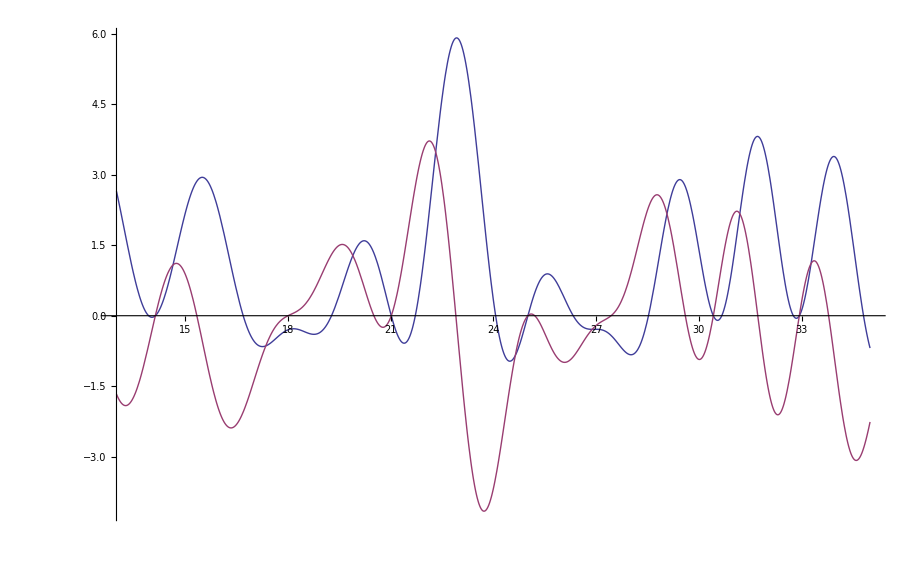

```mathematica
Plot[{Re[tt[1000,.5+I s]],Im[tt[1000,.5+I s]]},{s,13,35}]
```

```mathematica
N@tt[1000,ZetaZero[1]]
```

-4.87234×10^-6-8.24266×10^-7 ⅈ

```mathematica
po[8000000000,N@ZetaZero[3]]
```

-1771.17+242.715 ⅈ

```mathematica
2  2^N[-ZetaZero[3]] po[8000000000/2,N@ZetaZero[3]]
```

-1771.17+242.715 ⅈ

```mathematica
po[1000000000,N@ZetaZero[1]]
 2 2^N[ZetaZero[1]] po[1000000000/2,N@ZetaZero[1]]
```

```mathematica
tt[2,s]
```

1+3^-s+5^-s+7^-s+9^-s+11^-s+13^-s+15^-s-2^(1-s) (1+3^-s+5^-s+7^-s)

```mathematica
1+3^-s + 5^-s +7^-s - 2^-s -2^-s -6^-s - 6^-s/.s->.5+I
```

0.197926+0.387535 ⅈ

```mathematica
tt[1,.5+I]
```

0.197926+0.387535 ⅈ

```mathematica
Sum[ ff[n,s]2^-a,{a,Log[2,n],Infinity}]
```

(2 ff[n,s])/n

```mathematica
eet[n_,s_]:=Sum[ (-1)^(j+1) j^-s,{j,1,n}]
epo[n_,s_]:=Sum[ j^-s,{j,1,n,2}]
es2[n_,s_]:=po[n,s]-Sum[ (2^a)^-s po[n/(2^a),s],{a,1,Log2@n}]
es2a[n_,s_]:=Sum[ po[n,s]/2^a,{a,1,Infinity}]-Sum[ (2^a)^-s po[n/(2^a),s],{a,1,Log2@n}]
es2b[n_,s_]:=Sum[ po[n,s]/2^a,{a,Floor[Log2@n]+1,Infinity}]+Sum[ po[n,s]/2^a,{a,1,Floor[Log2@n]}]-Sum[ (2^a)^-s po[n/(2^a),s],{a,1,Log2@n}]
es2c[n_,s_]:=Sum[ po[n,s]/2^a,{a,Floor[Log2@n]+1,Infinity}]+Sum[ po[n,s]/2^a-(2^a)^-s po[n/(2^a),s],{a,1,Log2@n}]
es2d[n_,s_]:=Sum[ po[n,s]/2^a,{a,Floor[Log2@n]+1,Infinity}]+Sum[ 2^-a po[n,s]-(2^-a)^s po[n/(2^a),s],{a,1,Log2@n}]
es2e[n_,s_]:=Sum[ po[n,s]/2^a,{a,Floor[Log2@n]+1,Infinity}]+Sum[ 2^-a po[n,s]-(2^(-a s)) po[n/(2^a),s],{a,1,Log2@n}]
es2f[n_,s_]:=Sum[ po[n,s]/2^a,{a,Floor[Log2@n]+1,Infinity}]+Sum[ 2^-a Sum[ j^-s,{j,1,n,2}]-(2^(-a s)) Sum[ j^-s,{j,1,n/(2^a),2}],{a,1,Log2@n}]
es2g[n_,s_]:=Sum[ po[n,s]/2^a,{a,Floor[Log2@n]+1,Infinity}]+Sum[ Sum[2^-a  j^-s,{j,1,n,2}]- Sum[ (2^(-a s))j^-s,{j,1,n/(2^a),2}],{a,1,Log2@n}]
es2h[n_,s_]:=Sum[ po[n,s]/2^a,{a,Floor[Log2@n]+1,Infinity}]+Sum[ Sum[2^-a  j^-s,{j,1,n,2}]- Sum[ (2^(-a s))j^-s,{j,1,n/(2^a),2}],{a,1,Log2@n}]



N@eet[100,-1+13I]
```

51.9917-23.4411 ⅈ

```mathematica
N@es2h[100,-1+13I]
```

51.9917-23.4411 ⅈ

```mathematica
FullSimplify[(2^(-a))^s]
```

(2^-a)^s

```mathematica
(2^(3+I))^6
```

2^(18+6 ⅈ)

```mathematica
4^6
```

4096

```mathematica
2^12
```

4096

```mathematica
2^(-a s)
```

2^(-a s)

```mathematica
2^s 2^(-a)
```

2^(-a+s)

```mathematica
2^3 fn - 2^(3 a) gfn
```

8 fn-2^(3 a) gfn

```mathematica
tr[n_,s_,a_]:= Sum[2^-a  j^-s,{j,1,n,2}]- Sum[ (2^(-a s))j^-s,{j,1,n/(2^a),2}]
tr1[n_,s_]:= 1/2 Sum[ j^-s,{j,1,n,2}]- (1/2)Sum[2 j^-s(2^(-s)),{j,1,n/2,2}]
tr1a[n_,s_]:= 1/2( Sum[ j^-s,{j,1,n,2}]- Sum[ j^-s(2^(-s)),{j,1,n/2,2}]- Sum[ j^-s(2^(-s)),{j,1,n/2,2}])
tr1b[n_,s_]:= 1/2( Sum[ j^-s,{j,1,n,2}]- Sum[ j^-s(2^(-s)),{j,1,n/2,2}]- Sum[ j^-s(2^(-s)),{j,1,n/2,2}])
```

```mathematica
tr1b[1000000000,N@ZetaZero[1]]
```

5.78694×10^-6-5.38623×10^-6 ⅈ

```mathematica
tr1b[8,s]
```

1/2 (1-2^(1-s)+3^-s-2^(1-s) 3^-s+5^-s+7^-s)

```mathematica
N[-(2^(-ZetaZero[1]))]
```

0.658571-0.257458 ⅈ

```mathematica
zetar[n_,s_,a_]:= Sum[2^-a  j^-s,{j,1,n,2}]+ Sum[ (2^(-a s))j^-s,{j,1,n/(2^a),2}]
```

```mathematica
N@zetar[100000,2,1]
```

0.92527

```mathematica
N@tr[100000.,3,1]
```

0.394425

```mathematica
zt1[n_,s_]:=Sum[ N[j^-s],{j,1,Floor[n]}]
zt2[n_,s_]:=Sum[ N[j^-s],{j,1,Floor[n],2}]
zt3[n_,s_]:=Sum[ N[2^-k s],{k,0,Log2@n}]
zd1[n_,s_,r_]:= zt1[n,s]-r^(1-s)zt1[n/r,s]
zd2[n_,s_,r_]:= zt2[n,s]-r^(1-s)zt2[n/r,s]
zd3[n_,s_,r_]:= zt3[n,s]-r^(1-s)zt2[n/r,s]
```

```mathematica
N@zd1[10000000.0,N@ZetaZero[1],1.2]
```

-5.63043×10^-6-0.0000947011 ⅈ

```mathematica
Log[2.3]
```

0.832909

```mathematica
zt1[100000000.0,N@ZetaZero[1]]
```

239.497-665.237 ⅈ

```mathematica
N@zd2[100000000.0,1,3]
```

0.549306

```mathematica
N@zd3[1000000000.0,N[ZetaZero[1]],1.2]
```

791.103+819.146 ⅈ

```mathematica
pom[n_,s_]:=Sum[ j^-s,{j,1,Floor[n]}]
dif[n_, s_,a_,b_]:=(a^(1-s) pom[n/a,s])-(b^(1-s) pom[n/b,s])
div[n_, s_,a_,b_]:=(a^(1-s) pom[n/a,s])/(b^(1-s) pom[n/b,s])
(* If Re(s) > 1, the following is true *)
div2[n_,s_,a_,b_]:=(b/a)^(s-1)
```

```mathematica
N@dif[10^20,2,1,2]
```

0.822467

```mathematica
N@dif[10^20,.5,1,2]
```

0.604897

```mathematica
N@div[10^200,2+I,1,2]
```

1.53848+1.27792 ⅈ

```mathematica
N@div[10^24,1.1+I,3.2,5.4]
```

0.911603+0.52468 ⅈ

```mathematica
N@div2[10^24,1.1+I,3.2,5.4]
```

0.912731+0.526539 ⅈ

```mathematica
dif[10^20,1/2+I,1,2]
```

-2^(1/2-ⅈ) HarmonicNumber[50000000000000000000,1/2+ⅈ]+HarmonicNumber[100000000000000000000,1/2+ⅈ]

```mathematica
N[-2^(1/2-ⅈ)]
```

-1.08787+0.903628 ⅈ

```mathematica
dif[10^20,ZetaZero[1],1,2]
```

-2^(1-ZetaZero[1]) HarmonicNumber[50000000000000000000,ZetaZero[1]]+HarmonicNumber[100000000000000000000,ZetaZero[1]]

```mathematica
N[-2^(1-ZetaZero[1])]
```

1.31714-0.514916 ⅈ

```mathematica
5000000003^(.5+3I)
```

-36726.-60425.1 ⅈ

```mathematica
N[1-2^(1-ZetaZero[1])]
```

2.31714-0.514916 ⅈ

```mathematica
N[1-2^(1-ZetaZero[1])](5000000000-1)^(N[ZetaZero[1]])
```

46723.1+161209. ⅈ

```mathematica
(5000000000)^(N[ZetaZero[1]])
```

4482.35+70568.5 ⅈ

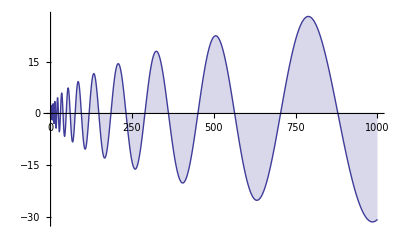

```mathematica
DiscretePlot[ { Re[x^N[ZetaZero[1]]]},{x,1,1000}]
```

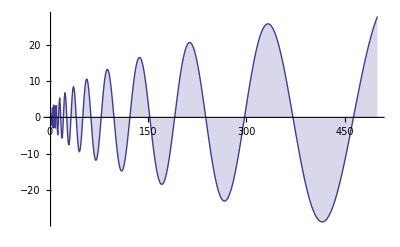

```mathematica
DiscretePlot[ Re[-2^(1-ZetaZero[1])x^N[ZetaZero[1]]],{x,1,500}]
```

```mathematica
Sum[MoebiusMu[j]/j HarmonicNumber[Floor[10/j]],{j,1,10}]
```

1

```mathematica
md[n_]:=Sum[MoebiusMu[j]/j (2),{j,1,n}]-Sum[MoebiusMu[j]/j (HarmonicNumber[Floor[n/j]]),{j,1,n}]
md2[n_]:=Sum[1/j (2-HarmonicNumber[Floor[n/j]]),{j,1,n}]
Table[md[n]-md[n-1] ,{n,1,12}]
```

{1,-1,-2/3,0,-2/5,1/3,-2/7,0,0,1/5,-2/11,0}

```mathematica
Table[If[n==1,-1,0]+2 MoebiusMu[n]/n ,{n,1,12}]
```

{1,-1,-2/3,0,-2/5,1/3,-2/7,0,0,1/5,-2/11,0}

```mathematica
Clear[pe]
pe[n_,k_]:=pe[n,k]=Sum[ (If[j==1,-1,0]+2 MoebiusMu[j]/j) pe[n-j,k-1],{j,1,n-1}]
pe[n_,1]:=(If[n==1,-1,0]+2 MoebiusMu[n]/n)
pe[n_,0]:=If[n==0,1,0]
pa[n_,z_]:=Sum[ z^k/k! pe[n,k],{k,0,n}]
```

```mathematica
Table[pa[n,1],{n,1,12}]
```

{1,-1/2,-3/2,-5/8,11/40,181/240,589/1680,-2869/13440,-2843/8064,103751/403200,677791/4435200,-3547517/17740800}

```mathematica
Table[md[n] ,{n,1,12}]
```

{1,0,-2/3,-2/3,-16/15,-11/15,-107/105,-107/105,-107/105,-86/105,-1156/1155,-1156/1155}

```mathematica
Sum[ md[Floor[12/j]]/j,{j,1,12}]
```

-30581/27720

```mathematica
2-HarmonicNumber[12]
```

-30581/27720

```mathematica
Sum[MoebiusMu[j] md2[Floor[12/j]]/j,{j,1,12}]
```

-30581/27720

```mathematica
Clear[pe,pp]
pe[n_,k_]:=pe[n,k]=Sum[ -(2^j-1)/j  pe[n-j,k-1],{j,1,n-1}]
pe[n_,1]:=-(2^n-1)/n
pe[n_,0]:=If[n==0,1,0]
pa[n_,z_]:=Sum[ z^k/k! pe[n,k],{k,0,n}]
pp[n_,k_]:=pp[n,k]=Sum[ - pp[n-j,k-1],{j,1,n-1}]
pp[n_,0]:=If[n==0,1,0]
pp[n_,1]:=-1
pss[n_,z_]:=Sum[ bin[z,k] pp[n,k],{k,0,n}]
```

```mathematica
Table[D[pss[n,z],z]/.z->0,{n,0,12}]
```

{0,-1,-3/2,-7/3,-15/4,-31/5,-21/2,-127/7,-255/8,-511/9,-1023/10,-2047/11,-1365/4}

```mathematica
FullSimplify[2-Sum[x^k,{k,0,Infinity}]]
```

2+1/(-1+x)

```mathematica
Series[2-1/(1-x),{x,0,10}]
```

1-x-x^2-x^3-x^4-x^5-x^6-x^7-x^8-x^9-x^10+O[x]^11

```mathematica
Integrate[ 1-x-x^2-x^3,x]
```

x-x^2/2-x^3/3-x^4/4

```mathematica
Table[-(2^n-1)/n,{n,0,12}]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

{Indeterminate,-1,-3/2,-7/3,-15/4,-31/5,-21/2,-127/7,-255/8,-511/9,-1023/10,-2047/11,-1365/4}

```mathematica
Table[pa[n,1],{n,0,12}]
```

{1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
Ak[n_]:=Sum[ -(2^j-1)/j ,{j,1,n}]
invAk[n_]:=Sum[ MoebiusMu[j]/j Ak[Floor[n/j]],{j,1,n}]
invAk2[n_]:=Sum[ invAk[Floor[n/j]]/j,{j,1,n}]
```

```mathematica
(* https://oeis.org/A097344 *)
```

```mathematica
Table[Ak[n],{n,1,10}]
```

{-1,-5/2,-29/6,-103/12,-887/60,-1517/60,-18239/420,-63253/840,-332839/2520,-118127/504}

```mathematica
Table[HypergeometricPFQ[{1,1,-n},{2,2},-1]//Numerator,{n,0,12}]
```

{1,5,29,103,887,1517,18239,63253,332839,118127,2331085,4222975,100309579}

```mathematica
Table[invAk[n]-invAk[n-1],{n,1,20}]
```

{-1,-1,-2,-3,-6,-9,-18,-30,-56,-99,-186,-335,-630,-1161,-2182,-4080,-7710,-14532,-27594,-52377}

```mathematica
Table[invAk2[n]-invAk2[n-1],{n,1,10}]
```

{-1,-3/2,-7/3,-15/4,-31/5,-21/2,-127/7,-255/8,-511/9,-1023/10}

```mathematica
(* https://oeis.org/A059966 *)
```

```mathematica
Table[1/n Apply[Plus,Map[(MoebiusMu[n/#](2^#-1))&,Divisors[n]]],{n,1,20}]
```

{1,1,2,3,6,9,18,30,56,99,186,335,630,1161,2182,4080,7710,14532,27594,52377}

```mathematica
Clear[pe]
pe[n_,k_]:=pe[n,k]=Sum[ (invAk[j]-invAk[j-1])  pe[n-j,k-1],{j,1,n-1}]
pe[n_,1]:=invAk[n]-invAk[n-1]
pe[n_,0]:=If[n==0,1,0]
pa[n_,z_]:=Sum[ z^k/k! pe[n,k],{k,0,n}]
```

```mathematica
Table[pa[n,-1],{n,1,20}]
```

{1,3/2,19/6,145/24,507/40,17491/720,251203/5040,1325483/13440,14365325/72576,1431651331/3628800,10531651057/13305600,756534213073/479001600,19695041269489/6227020800,4082229886613/645765120,16536564083960131/1307674368000,529078125772064641/20922789888000,5997196382277344171/118562476032000,49816223747401636303/492490285056000,4922208068556923587127/24329020081766400,328132653266986162905307/810967336058880000}

```mathematica
Series[(1-2x)/(1-x),{x,0,10}]
```

1-x-x^2-x^3-x^4-x^5-x^6-x^7-x^8-x^9-x^10+O[x]^11

```mathematica
Product[ ((1-2x)/(1-x))^( MoebiusMu[k]/k),{k,1,10}]
```

(1-2 x)/(((1-2 x)/(1-x))^(191/210) (1-x))

```mathematica
Clear[pq,n,Pq]
arb[n_]:=Sum[ MoebiusMu[n/d]((2^d)-1)/n,{d,Divisors[n]}]
pq[1]:=-1
pq[2]:=-1
pq[n_]:=pq[n]=Floor[MangoldtLambda[n]/Log[n]]-If[Log[2,n]==Floor[Log[2,n]],arb[Log[2,n]],0]
Pq[n_,k_]:=Pq[n,k]=Sum[ pq[j]Pq[Floor[n/j],k-1],{j,2,n}]
Pq[n_,0]:=UnitStep[n-1]
pqz[n_,z_]:=Sum[ z^k/k! Pq[n,k],{k,0,Log2@n}]
```

```mathematica
Table[pq[n]-(pm[n,0]-pm[n-1,0]),{n,2,100}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[pqz[n,1],{n,1,100}]
```

{1,0,1,1/2,3/2,1/2,3/2,1/3,5/6,-1/6,5/6,1/3,4/3,1/3,4/3,3/8,11/8,7/8,15/8,11/8,19/8,11/8,19/8,29/24,41/24,17/24,7/8,3/8,11/8,3/8,11/8,-29/30,1/30,-29/30,1/30,-13/60,47/60,-13/60,47/60,-23/60,37/60,-23/60,37/60,7/60,37/60,-23/60,37/60,-41/120,19/120,-41/120,79/120,19/120,139/120,119/120,239/120,33/40,73/40,33/40,73/40,53/40,93/40,53/40,73/40,101/144,245/144,101/144,245/144,173/144,317/144,173/144,317/144,233/144,377/144,233/144,305/144,233/144,377/144,233/144,377/144,239/144,245/144,101/144,245/144,173/144,317/144,173/144,317/144,149/144,293/144,221/144,365/144,293/144,437/144,293/144,437/144,499/720,1219/720,859/720,1219/720,1039/720}